### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/14

### Keywords

Details

# Model 1.4

Model 1.4 is the dynamics model of malaria parasites at asexulal stage in an infected host. It was proposed by N.J. White, et. al., (1992) (The effects of multiplication and synchronicity on the vascular distribution of parasites in falciparum malaria Transactions of the Royal Society of Tropical Medicine and Hygiene 86, 590-597). The model assume all parasites have the same multiplication rate at every life-cycle and grow with the same speed. The parasites have the age distribution following a normal distribution at the beginning of the model.

model | the model ID
initn | the initial number of parasites
lifecycle | the parasites life-cycle (hours)
mu | the mean age of parasites (hours) at the beginning of the model.
sigma | the standard deviation of the parastite ages (hours) at the beginning of the model
pmr | the parasite multiplication rate (per life-cycle)
endage | the end of the age of paraises for.
runmax | the maximum runtime of the model (hours)
outform | the output form

List of the parameters of model 1.4.

Model 1.4 has three output form. See table below.

0 | show the list of number of parasites at the ages 1-endage of every time steps (from 0 - runmax)
1 | show the list of total number of parasites over time (from 0 - runmax)
2 | show the list of total number of parasites (log10) over time (from 0 - runmax)

The values of outform for model 1.4.

The example of the output of model 1.4

******INDIVARIA*****

model: 1.4

outform: 2

********************

model: 1.4

initn: 6.02*10^4

lifecycle: 48

mu: 13

sigma: 8

pmr: 12

endage: 26

runmax: 240

outform: 2

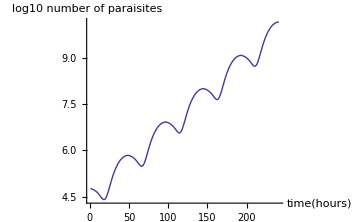

```mathematica
ListPlot[IDVL["mod1_4.in"],Joined->True,AxesLabel->{"time(hours)","log10 number of paraisites"}]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses